```mathematica
Get["C:\\Users\\douwm\\repos\\wolfram_summer_school\\2d_toolbox.wl"]
```

#### For a specific robot structure that consists only of triangles with no redundant modules and having one of 2 possible states for each module (long or short)

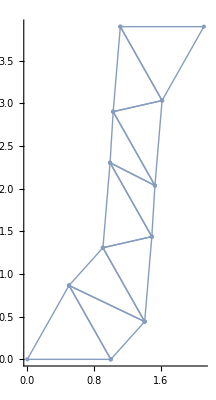

```mathematica
nrods =20;
shortlength = 0.6;
longlength = 1;
coords = MakeTriangleWorm[{0,0},{1,0}, RandomChoice[{shortlength,longlength},nrods]];
MeshAllTriag[coords,All]
```

#### If there are a large number of rods, collisions between rods tend to occur that can be detected

Did a collision occur?

True

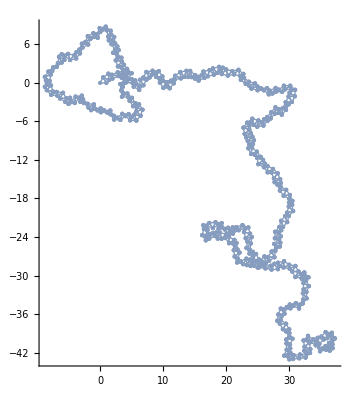

```mathematica
nrods =1000;
shortlength = 0.6;
longlength = 1;
coords = MakeTriangleWorm[{0,0},{1,0}, RandomChoice[{shortlength,longlength},nrods]];
Echo["Did a collision occur?"];
Echo[CollisionQ[coords,shortlength]];
MeshAllTriag[coords,All]
```

#### We can get an idea of the expected workspace of the mechanism (where the final point in the mechanism could go) by trying a series of random rod lengths

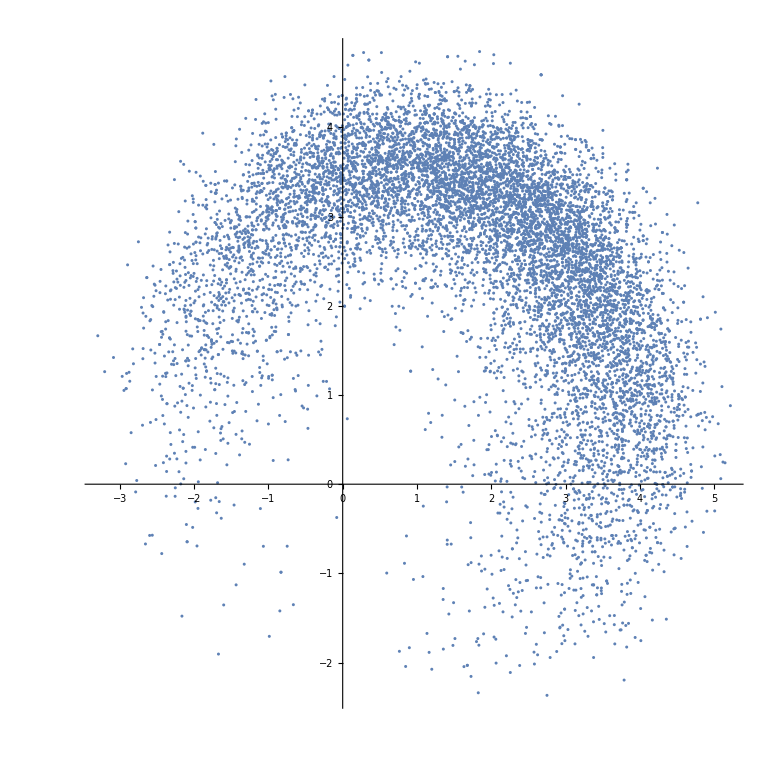

```mathematica
nrods =20;
shortlength = 0.6;
longlength = 1;
coords = Table[MakeTriangleWorm[{0,0},{1,0}, RandomChoice[{shortlength,longlength},nrods]],10000];
endeffector = coords[[All,-1,All]];
ListPlot[endeffector,PlotRange->All,AspectRatio->1]
```

#### Transitioning from a random state to its neighbour and then its neighbours’ neighbours.

a possible state {initial condition}

{0.6,0.6,0.6,0.6,1,1,1,0.6,1,1,1,0.6,1,0.6,1,0.6,1,1,1,1,1,0.6,0.6,0.6,0.6,1,1,1,1,0.6,1,0.6,0.6,0.6,1,0.6,1,1,1,1,1,0.6,0.6,1,0.6,0.6,0.6,0.6,0.6,1}

initial condition neighbours

First neighbours' neighbours

{1,0.6,1,1,1,0.6,0.6,0.6,1,0.6,0.6,0.6}

a possible state {initial condition}

{0.6,0.6,1,1,1,0.6,0.6,1,1,0.6,1,1}

initial condition neighbours

(1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
0.6 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
0.6 | 0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
0.6 | 0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 1 | 0.6 | 1 | 1
0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1
0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1
0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1
0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 1
0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 1
0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 0.6)

First neighbours' neighbours

(0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
1 | 0.6 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
1 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 1 | 0.6 | 1 | 1
1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1
1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1
1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1
1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 1
1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 1
1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 0.6)

-Graphics-

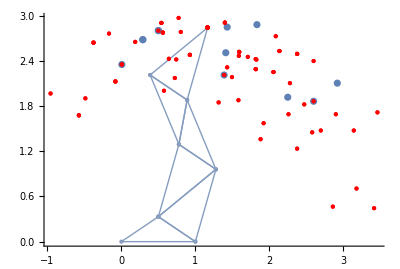

```mathematica
nc = MakeTriangleWorm[fixed1,fixed2,#]&/@ns;
nnc = MakeTriangleWorm[fixed1,fixed2,#]&/@Flatten[nns,1];
ne = nc[[All,-1,All]];
nne = nnc[[All,-1,All]];

g2 =Show[MeshAllTriag[MakeTriangleWorm[fixed1,fixed2,possiblestate],All],ListPlot[ne],ListPlot[nne,PlotStyle->{PointSize[Medium],Red}]]
```

#### Transition between all states

```mathematica
nrods=8;
shortlength=0.6;
longlength=1;
allstates=Tuples[{shortlength,longlength},nrods];
Graph[Flatten[StateToNeighbours[#,Black]&/@allstates]]
```

-Graphics-